Metody numeryczne, Informatyka NS sem. III, 2023/2024

Andrzej Manderla

# Projekt 6 – metoda Rungego-Kutty

## KOD

```mathematica
rk3Method[f_,a_,b_,y0_,n_]:=Module[{h=(b-a)/n,x=a,y=y0,xValues={a},yValues={y0},k1,k2,k3},Do[k1=h f[x,y];
k2=h f[x+0.5 h,y+0.5 k1];
k3=h f[x+h,y-k1+2 k2];
y+=(k1+4 k2+k3)/6;
x+=h;
AppendTo[xValues,x];
AppendTo[yValues,y];,{i,1,n}];
{xValues,yValues}];

rk4Method[f_,a_,b_,y0_,n_]:=Module[{h=(b-a)/n,x=a,y=y0,xValues={a},yValues={y0},k1,k2,k3,k4},Do[k1=h f[x,y];
k2=h f[x+0.5 h,y+0.5 k1];
k3=h f[x+0.5 h,y+0.5 k2];
k4=h f[x+h,y+k3];
y+=(k1+2 k2+2 k3+k4)/6;
x+=h;
AppendTo[xValues,x];
AppendTo[yValues,y];,{i,1,n}];
{xValues,yValues}];

rkMethod[f_,a_,b_,y0_,n_]:=Module[{sol,rk3,rk4,xValues},sol=DSolve[{y'[x]==f[x,y[x]],y[a]==y0},y[x],x][[1,1,2]];
rk3=rk3Method[f,a,b,y0,n];
rk4=rk4Method[f,a,b,y0,n];
xValues=rk3[[1]];
Print[Show[Plot[sol,{x,a,b},PlotStyle->Blue,PlotRange->All,ImageSize->Large],ListPlot[{Transpose[{xValues,rk3[[2]]}],Transpose[{xValues,rk4[[2]]}]},PlotStyle->{Red,Green},PlotMarkers->Automatic],PlotLabel->"Rozwiązania",AxesLabel->{"x","y"},PlotRange->All,ImageSize->Large]];
Print[Show[ListLinePlot[{Transpose[{xValues,Abs[rk3[[2]]-(sol/. x->#&/@xValues)]}],Transpose[{xValues,Abs[rk4[[2]]-(sol/. x->#&/@xValues)]}]},PlotStyle->{Red,Green},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large],PlotLabel->"Błędy bezwzględne",AxesLabel->{"x","Błąd"}]];];
```

## Przykłady

### Przykład z przykładowych przykładów.

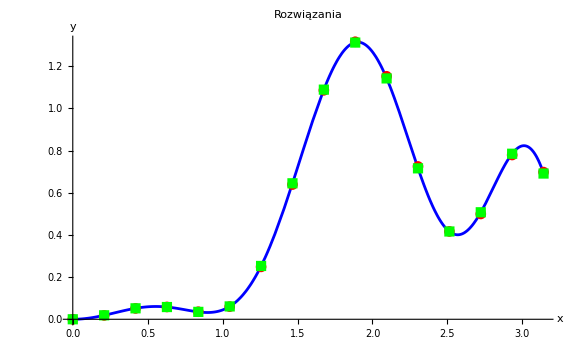

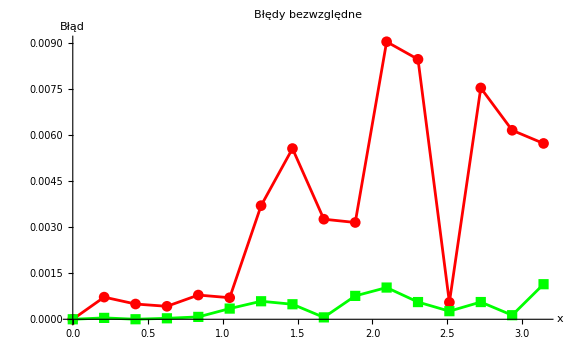

```mathematica
f[x_,y_]:=E^x Sin[x]Cos[2x]^2-3y;
rkMethod[f,0,Pi,0,15]
```

### Przykład własny.

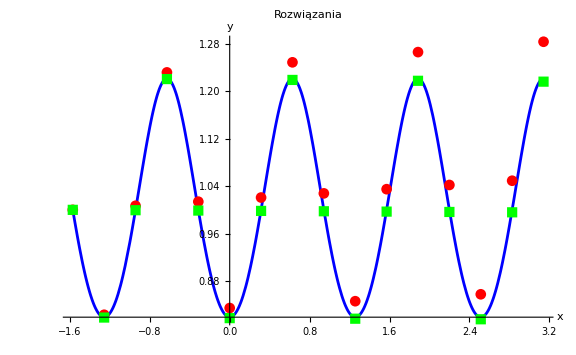

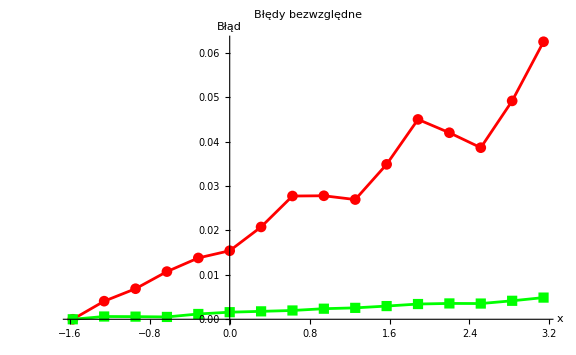

```mathematica
f[x_,y_]:=y Sin[5x];
rkMethod[f,-Pi/2,Pi,1,15]
```